```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
```

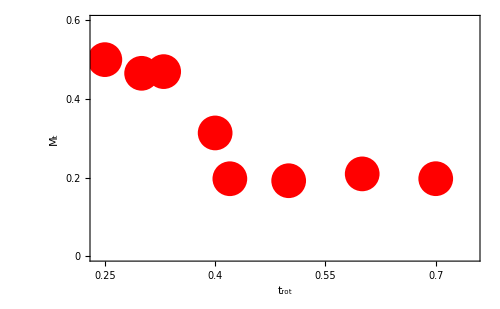

```mathematica
tvaluedattotalmt={0.25,0.3,0.33,0.4,0.42,0.5,0.6,0.7};

momentax=Table[Total[Flatten[ Import[StringJoin["trot_",ToString[tvalue],"_allmtax.dat"]][[1]][[{1,5,9}]]]],{tvalue,tvaluedattotalmt}];
momentbx=Table[Total[Flatten[ Import[StringJoin["trot_",ToString[tvalue],"_allmtbx.dat"]][[1]][[{1,5,9}]]]],{tvalue,tvaluedattotalmt}];


mgdata=Table[{tvaluedattotalmt[[i]],((momentax+momentbx)/2)[[i]]},{i,1,Length[tvaluedattotalmt]}];

mgplot=ListPlot[mgdata,Frame->True,FrameStyle->Directive[Thickness[0.005],Black,32],Epilog->{{Red,PointSize[0.05],Point[mgdata]}},PlotRange->{{0.24,0.75},{0,0.6}},
FrameTicks->{{{{0,0,0.03},{0.2,0.2,0.03},{0.4,0.4,0.03},{0.6,0.6,0.03}},{{0,Null,0.03},{0.2,Null,0.03},{0.4,Null,0.03},{0.6,Null,0.03}}},{{{0.25,0.25,0.03},{0.4,0.4,0.03},{0.55,0.55,0.03},{0.7,0.7,0.03}},{{0.25,Null,0.03},{0.4,Null,0.03},{0.55,Null,0.03},{0.7,Null,0.03}}}},
FrameLabel->{{Style["M_t",35,FontFamily->"TimesNewRoman"],None},{Style["t_rot",35,FontFamily->"TimesNewRoman"],None}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,40]},
ImagePadding->{{90,15},{90,17}},ImageSize->500]
Export["mgplot.eps",mgplot];
```